```mathematica
link = Install[NotebookDirectory[]<>"FreewayAC_Mathematica"]
```

LinkObject[…]

```mathematica
CreateCircularCA[100,5,0.5,0.2,1]
CAEvolve[100]
```

```mathematica
ca = CAGetHistory[]
```

{1}
 |  |  |  |

```mathematica
ca+1
```

{{0,2,2,0,0,0,0,0,2,2,0,2,2,0,0,0,2,2,2,2,2,0,2,2,0,0,2,2,2,0,2,0,0,2,0,2,2,0,2,2,0,0,2,2,0,2,2,0,2,0,0,2,0,2,2,2,2,2,2,2,0,2,0,2,2,0,0,2,0,0,0,2,2,0,2,2,2,0,0,0,0,2,0,0,0,0,0,0,2,0,0,2,0,2,0,0,2,0,0,2},99,{0,2,1,0,0,2,0,0,3,0,0,0,76,0,2,0,2,1,1,0,0,0,3,1,0}}
 |  |  |  |

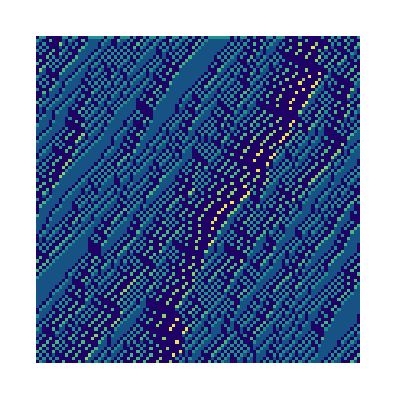

```mathematica
ArrayPlot[ca,ColorFunction->"BlueGreenYellow"]
```

```mathematica
CAGetCurrent[]
```

{-1,1,0,-1,-1,1,-1,-1,2,-1,-1,-1,-1,2,-1,0,0,-1,1,0,-1,1,0,-1,1,-1,1,-1,-1,-1,2,-1,-1,2,-1,-1,-1,3,-1,-1,-1,3,-1,-1,1,0,-1,0,0,-1,1,-1,-1,2,-1,1,-1,1,0,0,-1,-1,0,0,-1,0,0,-1,0,-1,1,-1,1,-1,1,-1,1,0,-1,1,-1,1,0,-1,1,0,0,0,-1,1,-1,1,0,0,-1,-1,-1,2,0,-1}